## 1.naloga

```mathematica
(x^5-2 x^2+3x+4)/(x^5-2x-1) /.x->{1,2,3,4}
```

{-3,34/27,119/118,144/145}

```mathematica
f[x_]:=(x^5-2 x^2+3x+4)/(x^5-2x-1)
```

```mathematica
f[x]/.x->{1,2,3,4}
```

{-3,34/27,119/118,144/145}

```mathematica
Table[f[x],{x,1,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

## 2. naloga

```mathematica
sez:={10,20,30,40,50,60,70}
```

```mathematica
sez[[{1,2,3}]]
```

{10,20,30}

```mathematica
Take[sez,-2]
```

{60,70}

```mathematica
Take[sez,{2,4}]
```

{20,30,40}

```mathematica
Part[sez,{2,3,5}]
```

{20,30,50}

```mathematica
Drop[sez,{4,5}]
```

{10,20,30,60,70}

## 3. naloga

```mathematica
sez:={x^6,x^2,a}
```

```mathematica
sez/.{{x->3},{x->x^2},{x^2->x},{x->{1,2,3}},{x->3,a->x}}
```

{{729,9,a},{x^12,x^4,a},{x^6,x,a},{{1,64,729},{1,4,9},a},{729,9,x}}

```mathematica
sez//.{x->3,a->x}
```

{729,9,3}

## 4. naloga

```mathematica
Clear[f[x]]
```

Clear::ssym: f[x] is not a symbol or a string.

```mathematica
res =D[x^5+4 x^3-9,x]
```

12 x^2+5 x^4

```mathematica
D[res,x]/.x->{1,5}
```

{44,2620}

```mathematica
g[x_]:=ⅇ^(x^(1/4))
```

```mathematica
odv = D[g[x],x]
```

(ⅇ^(x^(1/4)))/(4 x^(3/4))

```mathematica
odv/.x->{1,2}
```

{ⅇ/4,(ⅇ^(2^(1/4)))/(4 2^(3/4))}

```mathematica
h[x_]:=Abs[x+1]
```

```mathematica
odv1=FullSimplify[D[Abs[x+1],x],x ∈ Reals]
```

Sign[1+x]

```mathematica
odv1/.x->{1,-1}
```

{1,0}

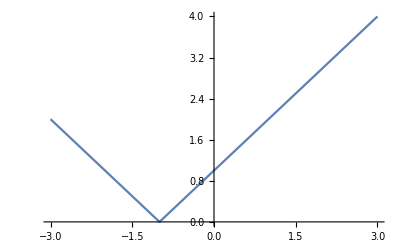

```mathematica
Plot[h[x],{x,-3,3}]
```

```mathematica
l[x_]:=a*x^2+3*b
```

```mathematica
D[l[x],x]/.x->{1,2}
```

{2 a,4 a}

### 5.naloga

```mathematica
ClearAll[f[x],f[x_]]
```

ClearAll::ssym: f[x] is not a symbol or a string.

ClearAll::ssym: f[x_] is not a symbol or a string.

```mathematica
f[x_]:=x^3 Log[4x+5]
```

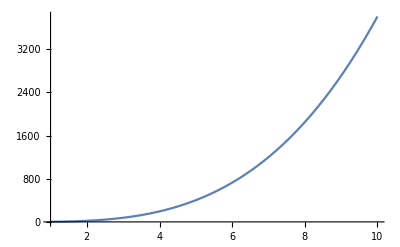

```mathematica
Plot[f[x],{x,1,10}]
```

```mathematica
n0=f[5]
```

125 Log[25]

```mathematica
N[125 Log[25]]
```

402.359

```mathematica
k0=D[f[x],x]/.x->5
```

20+75 Log[25]

```mathematica
N[k0]
```

261.416

```mathematica
t[x_]:=k0*x+n0
```

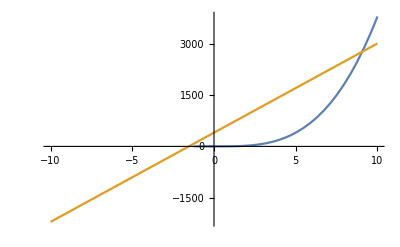

```mathematica
Plot[{f[x],t[x]},{x,-10,10}]
```

```mathematica
narisi[x0]:=Module[{k0,n0,t},
k0=D[f[x],x/.x->x0;
n0=n/.First[Solve[f[x0]=k0*x0+n,n]];
t[x_]:=k0*k+n0;
Plot[{f[x],t[x]},{x, 1, 10}]
]
```

### 6. naloga

```mathematica
Limit[(x^3-4 x^2+2x+4)/(x^5-9x-14),x->2]
```

-2/71

```mathematica
Limit[ArcTan[7x]/ArcSin[8x],x->0]
```

7/8

```mathematica
Limit[
```